```mathematica
(* INTENSITY PLOTS OF SCALAR SURFACE FROZEN WAVES FOR
  LOSSY OR LOSLESS MEDIA CALCULATED BY SFWI APPLICATION *)
```

```mathematica
(* Turn off labels of output cells (Out[]) *)
Quiet[SetOptions[Cell,ShowCellLabel-> False]]

(* Function to collect sfw parameters given a name of a file generated by sfwi application *)
LoadSfwParameters[FileInt_]:={
ClearAll[SfwComments,nr,ni,l0,Q,NN,L,P,CutAxis,CutValue,xmin,xmax,xpoints,ymin,ymax,ypoints,zmin,zmax,zpoints,data,FileIntPath];
FileIntPath=NotebookDirectory[]<>FileInt;
SfwComments=StringSplit[Import[FileIntPath,"Comments"][[2]]," "];
nr=Interpreter["Number"][SfwComments[[1]]];
ni=Interpreter["Number"][SfwComments[[2]]];
l0=Interpreter["Number"][SfwComments[[3]]];
Q=Interpreter["Number"][SfwComments[[4]]];
NN=Interpreter["Number"][SfwComments[[5]]];
L=Interpreter["Number"][SfwComments[[6]]];
P=Interpreter["Number"][SfwComments[[7]]];
H=Interpreter["Number"][SfwComments[[8]]];
CutAxis=Interpreter["String"][SfwComments[[9]]];
CutValue=Interpreter["Number"][SfwComments[[10]]];
xmin=Interpreter["Number"][SfwComments[[11]]];
xmax=Interpreter["Number"][SfwComments[[12]]];
xpoints=Interpreter["Number"][SfwComments[[13]]];
ymin=Interpreter["Number"][SfwComments[[14]]];
ymax=Interpreter["Number"][SfwComments[[15]]];
ypoints=Interpreter["Number"][SfwComments[[16]]];
zmin=Interpreter["Number"][SfwComments[[17]]];
zmax=Interpreter["Number"][SfwComments[[18]]];
zpoints=Interpreter["Number"][SfwComments[[19]]];
IsResistant=Interpreter["Number"][SfwComments[[20]]];
data=Import[FileIntPath];
};

(* Get pixels in L and H of binarized F *)
Quiet[LoadSfwParameters["F.mtx"]];
pxH=Dimensions[data][[1]];
pxL=Dimensions[data][[2]];

(* Normalization, sizes and font label for plots *)

LoadSfwParameters["int_xE[0,H,2P]_yE[0,10spot,P]_zE[1Ld4].mtx"];
MyTicksX={{0,0},{100xmax/4,NumberForm[100xmax/4,1]},{100 2xmax/4,NumberForm[100 2xmax/4,1]},{100 3xmax/4,NumberForm[100 3xmax/4,2]},{100xmax,NumberForm[100xmax,2]}}

LoadSfwParameters["int_xE[0,H,2P]_yE[0,10spot,P]_zE[1Ld4].mtx"];
MyTicksY={{-10000 ymax,-DecimalForm[10000 ymax,2]},{-10000 ymax/2,-DecimalForm[10000 ymax/2,2]},{0,0},{10000 ymax/2,DecimalForm[10000 ymax/2,2]},{10000 ymax,DecimalForm[10000 ymax,2]}}
LoadSfwParameters["int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[1Ld4].mtx"];
MyTicksY2={{-100 ymax,-DecimalForm[100 ymax,1]},{-100 ymax/2,-DecimalForm[100 ymax/2,2]},{0,0},{100 ymax/2,DecimalForm[100 ymax/2,2]},{100 ymax,DecimalForm[100 ymax,1]}}

LoadSfwParameters["int_xE[0,H,2P]_yE[0]_zE[0,L,pxL].mtx"];
MyTicksZ= {0.0,1.0,2.0,3.0,4.0,5.0,6.0}
sfwxzCentral=data;
MyColorData={"AvocadoColors",{0,Max[sfwxzCentral]}};
MyLabelStyle = {FontFamily->"Euclid",FontSize->32,FontWeight->"Plain",FontColor-> Black};
My2dImageSize=xpoints pxL/pxH;
My2dPlotSize=600;
MyBarLegend=BarLegend[MyColorData,LabelStyle->MyLabelStyle,LegendMarkerSize->{20,My2dPlotSize/2.8}];
```

{{0,0},{0.395705,0.4},{0.79141,0.8},{1.18712,1.2},{1.58282,1.6}}

{{-0.864004,-0.86},{-0.432002,-0.43},{0,0},{0.432002,0.43},{0.864004,0.86}}

{{-0.791411,-0.8},{-0.395706,-0.4},{0,0},{0.395706,0.4},{0.791411,0.8}}

{0.,1.,2.,3.,4.,5.,6.}

```mathematica
(* PLOTS *)
```

```mathematica
Quiet[LoadSfwParameters["F.mtx"]];
Export[FileIntPath<>".image.png",MatrixPlot[Reverse[data],AspectRatio->pxH/pxL,Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{1,1},{pxL,1},{pxL,pxH},{1,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{{1,22,pxH},None},{{1,82,pxL},None}},
Frame-> True,PlotLabel->"|F(x,z)|",FrameLabel->{"z (px)","x (px)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize,AspectRatio->pxH/pxL]}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[0]_zE[0,L,pxL].mtx"];
Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxL,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{0.,0.},{100.L,0.},{100.L,100.H},{0.,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksZ,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y=0,z)|^2",FrameLabel->{"z (cm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize,AspectRatio->pxH/pxL],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[5spot]_zE[0,L,pxL].mtx"];
Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxL,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{0.,0.},{100.L,0.},{100.L,100.H},{0.,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksZ,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y=5Δρ_LFW,z)|^2",FrameLabel->{"z (cm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize,AspectRatio->pxH/pxL],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[10spot]_zE[0,L,pxL].mtx"];
Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxL,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{0.,0.},{100.L,0.},{100.L,100.H},{0.,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksZ,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y=10Δρ_LFW,z)|^2",FrameLabel->{"z (cm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize,AspectRatio->pxH/pxL],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[1Hd4]_zE[0,L,pxL].mtx"];
Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxL,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{0.,0.},{100.L,0.},{100.L,100.H},{0.,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksZ,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y=H/4,z)|^2",FrameLabel->{"z (cm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize,AspectRatio->pxH/pxL],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[2Hd4]_zE[0,L,pxL].mtx"];
Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxL,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{0.,0.},{100.L,0.},{100.L,100.H},{0.,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksZ,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y=H/2,z)|^2",FrameLabel->{"z (cm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize,AspectRatio->pxH/pxL],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[0,10spot,P]_zE[1Ld4].mtx"];

data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];

Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxH,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize pxH/pxL,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{-10000.ymax,0.},{10000.ymax,0.},{10000.ymax,100.H},{-10000.ymax,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksY,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y,z=L/4)|^2",FrameLabel->{"y (μm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize ,AspectRatio->pxH/pxH],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[0,10spot,P]_zE[2Ld4].mtx"];

data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];

Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxH,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize pxH/pxL,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{-10000.ymax,0.},{10000.ymax,0.},{10000.ymax,100.H},{-10000.ymax,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksY,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y,z=L/2)|^2",FrameLabel->{"y (μm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize ,AspectRatio->pxH/pxH],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[0,10spot,P]_zE[3Ld4].mtx"];

data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];

Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxH,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize pxH/pxL,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{-10000.ymax,0.},{10000.ymax,0.},{10000.ymax,100.H},{-10000.ymax,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksY,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y,z=3L/4)|^2",FrameLabel->{"y (μm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize ,AspectRatio->pxH/pxH],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[1Ld4].mtx"];

data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];

Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxH,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize pxH/pxL,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{-100.ymax,0.},{100.ymax,0.},{100.ymax,100.H},{-100.ymax,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksY2,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y,z=L/4)|^2",FrameLabel->{"y (cm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize ,AspectRatio->pxH/pxH],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[2Ld4].mtx"];

data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];

Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxH,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize pxH/pxL,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{-100.ymax,0.},{100.ymax,0.},{100.ymax,100.H},{-100.ymax,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksY2,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y,z=L/2)|^2",FrameLabel->{"y (cm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize ,AspectRatio->pxH/pxH],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

```mathematica
LoadSfwParameters["int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[3Ld4].mtx"];

data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];

Export[FileIntPath<>".image.png",ListDensityPlot[data, PlotRange->All,AspectRatio->pxH/pxH,ColorFunctionScaling-> False,ColorFunction->ColorData[MyColorData],Axes->None,Frame->False,PlotRangePadding->None,ImageSize-> My2dImageSize pxH/pxL,ImageMargins->0]];
Export[FileIntPath<>".plot.pdf",
Grid[{{Show[Graphics[{Texture[Import[FileIntPath<>".image.png"]],Polygon[{{-100.ymax,0.},{100.ymax,0.},{100.ymax,100.H},{-100.ymax,100.H}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}],FrameTicks-> {{MyTicksX,None},{MyTicksY2,None}},
Frame-> True, PlotLabel->"|ψ_SFW(x,y,z=3L/4)|^2",FrameLabel->{"y (cm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->My2dPlotSize ,AspectRatio->pxH/pxH],
MyBarLegend}},
Alignment->{Center,Center}]
];
```

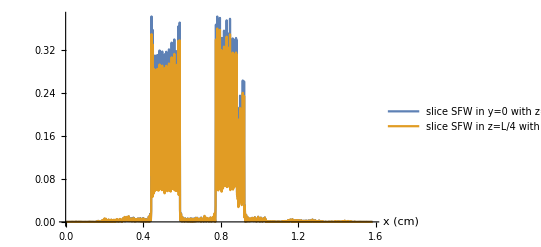
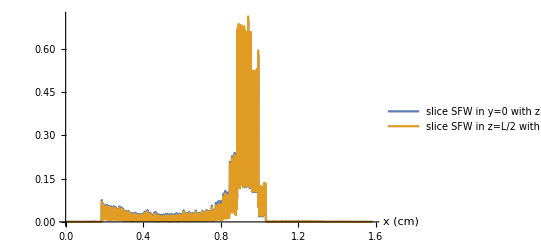
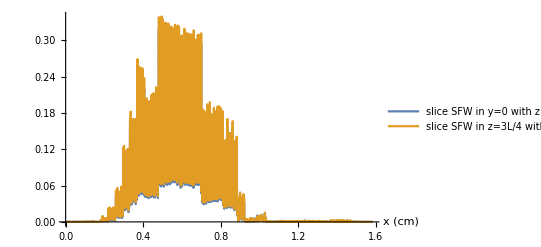
-Graphics- | -Graphics- | -Graphics-

```mathematica
(* PLOTS TO CHECK THE CONSISTENCY BETWEEN SLICES FOR -10 Subscript[Δρ, LFW]≤y≤10 Subscript[Δρ, LFW] *)
LoadSfwParameters["int_xE[0,H,2P]_yE[0,10spot,P]_zE[1Ld4].mtx"];
data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];
yEq0=Dimensions[data][[1]]/2;
zEqnLd4[n_]:=Ceiling[n(pxL-1)/4+1] (* return z = nL/4 proportional to points in z *)
gr1=ListLinePlot[{Transpose[sfwxzCentral][[zEqnLd4[1]]],Transpose[data][[yEq0]]},PlotRange->All,PlotLegends->Placed[{"slice SFW in y=0 with z=L/4","slice SFW in z=L/4 with y=0"},Bottom],AxesLabel->{"x (cm)"},DataRange->{0,100xmax}];

LoadSfwParameters["int_xE[0,H,2P]_yE[0,10spot,P]_zE[2Ld4].mtx"];
data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];
yEq0=Dimensions[data][[1]]/2;
zEqnLd4[n_]:=Ceiling[n(pxL-1)/4+1]
gr2=ListLinePlot[{Transpose[sfwxzCentral][[zEqnLd4[2]]],Transpose[data][[yEq0]]},PlotRange->All,PlotLegends->Placed[{"slice SFW in y=0 with z=L/2","slice SFW in z=L/2 with y=0"},Bottom],AxesLabel->{"x (cm)"},DataRange->{0,100xmax}];

LoadSfwParameters["int_xE[0,H,2P]_yE[0,10spot,P]_zE[3Ld4].mtx"];
data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];
yEq0=Dimensions[data][[1]]/2;
zEqnLd4[n_]:=Ceiling[n(pxL-1)/4+1]
gr3=ListLinePlot[{Transpose[sfwxzCentral][[zEqnLd4[3]]],Transpose[data][[yEq0]]},PlotRange->All,PlotLegends->Placed[{"slice SFW in y=0 with z=3L/4","slice SFW in z=3L/4 with y=0"},Bottom],AxesLabel->{"x (cm)"},DataRange->{0,100xmax}];

Grid[{{gr1,gr2,gr3}}]
ClearAll[gr1,gr2,gr3];
```

```mathematica
(* 3D SLICE PLOT FOR -10 Subscript[Δρ, LFW]≤y≤10 Subscript[Δρ, LFW] *)

zEqnLd4[n_]:=Ceiling[n(pxL-1)/4+1] (* return z = nL/4 proportional to points in z *)

grsfwxz=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0]_zE[0,L,pxL].mtx.image.png"]],Opacity[0.35],EdgeForm@None,
Polygon[{{0,0,0},{pxL,0,0},{pxL,0,pxH},{0,0,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];
grsfwxz1=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[5spot]_zE[0,L,pxL].mtx.image.png"]],Opacity[0.3],EdgeForm@None,
Polygon[{{0,-pxH/4.,0},{pxL,-pxH/4.,0},{pxL,-pxH/4.,pxH},{0,-pxH/4.,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];
grsfwxzm1=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[5spot]_zE[0,L,pxL].mtx.image.png"]],Opacity[0.3],EdgeForm@None,
Polygon[{{0,pxH/4.,0},{pxL,pxH/4.,0},{pxL,pxH/4.,pxH},{0,pxH/4.,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];
grsfwxz2=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[10spot]_zE[0,L,pxL].mtx.image.png"]],Opacity[0.3],EdgeForm@None,
Polygon[{{0,-pxH/2.,0},{pxL,-pxH/2.,0},{pxL,-pxH/2.,pxH},{0,-pxH/2.,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,,ImageMargins->0];
grsfwxzm2=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[10spot]_zE[0,L,pxL].mtx.image.png"]],Opacity[0.3],EdgeForm@None,
Polygon[{{0,pxH/2.,0},{pxL,pxH/2.,0},{pxL,pxH/2.,pxH},{0,pxH/2.,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,,ImageMargins->0];
grsfw1Ld4=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,10spot,P]_zE[1Ld4].mtx.image.png"]],Opacity[0.35],EdgeForm@None,Polygon[{{zEqnLd4[1],pxH/2,0},{zEqnLd4[1],-pxH/2,0},{zEqnLd4[1],-pxH/2,pxH},{zEqnLd4[1],pxH/2,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];
grsfw2Ld4=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,10spot,P]_zE[2Ld4].mtx.image.png"]],Opacity[0.35],EdgeForm@None,
Polygon[{{zEqnLd4[2],0.5pxH,0},{zEqnLd4[2],-0.5 pxH,0},{zEqnLd4[2],-0.5pxH,pxH},{zEqnLd4[2],0.5pxH,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];
grsfw3Ld4=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,10spot,P]_zE[3Ld4].mtx.image.png"]],Opacity[0.35],EdgeForm@None,
Polygon[{{zEqnLd4[3],0.5pxH,0},{zEqnLd4[3],-0.5pxH,0},{zEqnLd4[3],-0.5pxH,pxH},{zEqnLd4[3],0.5pxH,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];

LoadSfwParameters["int_xE[0,H,2P]_yE[0,10spot,P]_zE[1Ld4].mtx"];(* To load xmin xmax ymin ymax L and H *)

Export[NotebookDirectory[]<>"int_xE[0,H]_yE[-10spot,10spot]_zE[0,L].plot.pdf",
Grid[{{
Show [grsfwxz,grsfwxz1,grsfwxzm1,grsfwxz2,grsfwxzm2,grsfw1Ld4,grsfw2Ld4,grsfw3Ld4,Axes-> True,Ticks-> {{{1,0},{1pxL/6,1 100 L/6},{2pxL/6,2 100L/6},{3pxL/6,3 100L/6},{4 pxL/6,4 100L/6},{5pxL/6,5 100L/6},{6 pxL/6,6 100L/6}},{{-pxH/2,-NumberForm[10000 ymax,2]},{0,0},{pxH/2,NumberForm[10000 ymax,2]}},{{1,0},{pxH/2,NumberForm[100 xmax/2,1]},{pxH,NumberForm[100xmax,2]}}},AxesEdge-> {{-1,-1},{-1,1},{-1,-1}}, PlotLabel->"|ψ_SFW(x,y,z)|^2",AxesLabel->{"z (cm)","y (μm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->2My2dPlotSize,BoxRatios->{pxL,pxH,pxH},Lighting-> {"Ambient",White,{0,0,0}},ImagePadding->{{170,20},{80,20}},PlotRangePadding-> 8,ViewPoint->{1.3,-2.4,2.}],
MyBarLegend}},Alignment->{Center,Center}]
];
```

```mathematica
(* ANIMATION FOR -10 Subscript[Δρ, LFW]≤y≤10 Subscript[Δρ, LFW] *)
(*LoadSfwParameters["int_xE[0,H,2P]_yE[0,10spot,P]_zE[1Ld4].mtx"];
SFW3D[t_?NumericQ]:=Show[grsfwxz,grsfwxz1,grsfwxz2,grsfwxzm1,grsfwxzm2,grsfw1Ld4,grsfw2Ld4,grsfw3Ld4,Axes-> True,Ticks-> {{{1,0},{1pxL/6,1 100 L/6},{2pxL/6,2 100L/6},{3pxL/6,3 100L/6},{4 pxL/6,4 100L/6},{5pxL/6,5 100L/6},{6 pxL/6,6 100L/6}},{{-pxH/2,-NumberForm[10000 ymax,2]},{0,0},{pxH/2,NumberForm[10000 ymax,2]}},{{1,0},{pxH/2,NumberForm[100 xmax/2,1]},{pxH,NumberForm[100xmax,2]}}},AxesEdge-> {{-1,-1},{-1,1},{-1,-1}}, PlotLabel->"|ψ_SFW(x,y,z)|^2",AxesLabel->{"z (cm)","y (μm)","x (cm)"},LabelStyle->MyLabelStyle,BoxRatios->{pxL,pxH,pxH},Lighting-> {"Ambient",White,{0,0,0}},PlotRangePadding-> 8,ImagePadding->{{170,170},{0,0}},ViewCenter-> Center,ViewVector->{5pxL Sin[t],5pxL Cos[t],4pxH},SphericalRegion->True,ImageSize->2My2dPlotSize]
anim=Table[SFW3D[t],{t,3π/4,11π/4,π/160}];
Export[NotebookDirectory[]<>"int_xE[0,H]_yE[-10spot,10spot]_zE[0,L].plot.gif",anim,"DisplayDurations"->0.10,"AnimationRepetitions"->Infinity];
ClearAll[anim,SFW3D];*)
```

```mathematica
(* PLOTS TO CHECK THE CONSISTENCY BETWEEN SLICES FOR -H/2≤y≤H/2 *)
LoadSfwParameters["int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[1Ld4].mtx"];
data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];
yEq0=Dimensions[data][[1]]/2;
zEqnLd4[n_]:=Ceiling[n(pxL-1)/4+1] (* z = nL/4 proportional to points in z *)
gr1=ListLinePlot[{Transpose[sfwxzCentral][[zEqnLd4[1]]],Transpose[data][[yEq0]]},PlotRange->All,PlotLegends->Placed[{"slice SFW in y=0 with z=L/4","slice SFW in z=L/4 with y=0"},Bottom],AxesLabel->{"x (cm)"},DataRange->{0,100xmax}];

LoadSfwParameters["int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[2Ld4].mtx"];
data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];
yEq0=Dimensions[data][[1]]/2;
zEqnLd4[n_]:=Ceiling[n(pxL-1)/4+1]
gr2=ListLinePlot[{Transpose[sfwxzCentral][[zEqnLd4[2]]],Transpose[data][[yEq0]]},PlotRange->All,PlotLegends->Placed[{"slice SFW in y=0 with z=L/2","slice SFW in z=L/2 with y=0"},Bottom],AxesLabel->{"x (cm)"},DataRange->{0,100xmax}];

LoadSfwParameters["int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[3Ld4].mtx"];
data = Table[If[jj≤ypoints,data[[ii,ypoints+1-jj]],data[[ii,jj-ypoints+1]]],{ii,1,xpoints},{jj,1,2ypoints-1}];
yEq0=Dimensions[data][[1]]/2;
zEqnLd4[n_]:=Ceiling[n(pxL-1)/4+1]
gr3=ListLinePlot[{Transpose[sfwxzCentral][[zEqnLd4[3]]],Transpose[data][[yEq0]]},PlotRange->All,PlotLegends->Placed[{"slice SFW in y=0 with z=3L/4","slice SFW in z=3L/4 with y=0"},Bottom],AxesLabel->{"x (cm)"},DataRange->{0,100xmax}];

Grid[{{gr1,gr2,gr3}}]
ClearAll[gr1,gr2,gr3];
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
(* 3D SLICE PLOT FOR -H/2≤y≤H/2 *)

zEqnLd4[n_]:=Ceiling[n(pxL-1)/4+1] (* z = nL/4 proportional to points in z *)

grsfwxz=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0]_zE[0,L,pxL].mtx.image.png"]],Opacity[0.35],EdgeForm@None,
Polygon[{{0,0,0},{pxL,0,0},{pxL,0,pxH},{0,0,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];
grsfwxz1=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[1Hd4]_zE[0,L,pxL].mtx.image.png"]],Opacity[0.3],EdgeForm@None,
Polygon[{{0,-pxH/4.,0},{pxL,-pxH/4.,0},{pxL,-pxH/4.,pxH},{0,-pxH/4.,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];
grsfwxzm1=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[1Hd4]_zE[0,L,pxL].mtx.image.png"]],Opacity[0.3],EdgeForm@None,
Polygon[{{0,pxH/4.,0},{pxL,pxH/4.,0},{pxL,pxH/4.,pxH},{0,pxH/4.,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];
grsfwxz2=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[2Hd4]_zE[0,L,pxL].mtx.image.png"]],Opacity[0.3],EdgeForm@None,
Polygon[{{0,-pxH/2.,0},{pxL,-pxH/2.,0},{pxL,-pxH/2.,pxH},{0,-pxH/2.,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,,ImageMargins->0];
grsfwxzm2=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[2Hd4]_zE[0,L,pxL].mtx.image.png"]],Opacity[0.3],EdgeForm@None,
Polygon[{{0,pxH/2.,0},{pxL,pxH/2.,0},{pxL,pxH/2.,pxH},{0,pxH/2.,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,,ImageMargins->0];
grsfw1Ld4=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[1Ld4].mtx.image.png"]],Opacity[0.35],EdgeForm@None,Polygon[{{zEqnLd4[1],pxH/2,0},{zEqnLd4[1],-pxH/2,0},{zEqnLd4[1],-pxH/2,pxH},{zEqnLd4[1],pxH/2,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];
grsfw2Ld4=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[2Ld4].mtx.image.png"]],Opacity[0.35],EdgeForm@None,
Polygon[{{zEqnLd4[2],0.5pxH,0},{zEqnLd4[2],-0.5 pxH,0},{zEqnLd4[2],-0.5pxH,pxH},{zEqnLd4[2],0.5pxH,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];
grsfw3Ld4=Graphics3D[{Texture[Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[3Ld4].mtx.image.png"]],Opacity[0.35],EdgeForm@None,
Polygon[{{zEqnLd4[3],0.5pxH,0},{zEqnLd4[3],-0.5pxH,0},{zEqnLd4[3],-0.5pxH,pxH},{zEqnLd4[3],0.5pxH,pxH}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImagePadding->None,ImageMargins->0];

LoadSfwParameters["int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[1Ld4].mtx"];

Export[NotebookDirectory[]<>"int_xE[0,H]_yE[-Hd2,Hd2]_zE[0,L].plot.pdf",
Grid[{{
Show [grsfwxz,grsfwxz1,grsfwxzm1,grsfwxz2,grsfwxzm2,grsfw1Ld4,grsfw2Ld4,grsfw3Ld4,Axes-> True,Ticks-> {{{1,0},{1pxL/6,1 100 L/6},{2pxL/6,2 100L/6},{3pxL/6,3 100L/6},{4 pxL/6,4 100L/6},{5pxL/6,5 100L/6},{6 pxL/6,6 100L/6}},{{-pxH/2,-NumberForm[100 ymax,2]},{0,0},{pxH/2,NumberForm[100 ymax,2]}},{{1,0},{pxH/2,NumberForm[100 xmax/2,1]},{pxH,NumberForm[100xmax,2]}}},AxesEdge-> {{-1,-1},{-1,1},{-1,-1}}, PlotLabel->"|ψ_SFW(x,y,z)|^2",AxesLabel->{"z (cm)","y (cm)","x (cm)"},LabelStyle->MyLabelStyle,ImageSize->2My2dPlotSize,BoxRatios->{pxL,pxH,pxH},Lighting-> {"Ambient",White,{0,0,0}},ImagePadding->{{170,20},{80,20}},PlotRangePadding-> 8,ViewPoint->{1.3,-2.4,2.}],
MyBarLegend}},Alignment->{Center,Center}]
];
```

```mathematica
(* ANIMATION FOR -H/2≤y≤H/2 *)
(*LoadSfwParameters["int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[1Ld4].mtx"];
SFW3D[t_?NumericQ]:=Show[grsfwxz,grsfwxz1,grsfwxz2,grsfwxzm1,grsfwxzm2,grsfw1Ld4,grsfw2Ld4,grsfw3Ld4,Axes-> True,Ticks-> {{{1,0},{1pxL/6,1 100 L/6},{2pxL/6,2 100L/6},{3pxL/6,3 100L/6},{4 pxL/6,4 100L/6},{5pxL/6,5 100L/6},{6 pxL/6,6 100L/6}},{{-pxH/2,-NumberForm[100 ymax,2]},{0,0},{pxH/2,NumberForm[100 ymax,2]}},{{1,0},{pxH/2,NumberForm[100 xmax/2,1]},{pxH,NumberForm[100xmax,2]}}},AxesEdge-> {{-1,-1},{-1,1},{-1,-1}}, PlotLabel->"|ψ_SFW(x,y,z)|^2",AxesLabel->{"z (cm)","y (cm)","x (cm)"},LabelStyle->MyLabelStyle,BoxRatios->{pxL,pxH,pxH},Lighting-> {"Ambient",White,{0,0,0}},PlotRangePadding-> 8,ImagePadding->{{170,170},{0,0}},ViewCenter-> Center,ViewVector->{5pxL Sin[t],5pxL Cos[t],4pxH},SphericalRegion->True,ImageSize-> 2My2dPlotSize]
anim=Table[SFW3D[t],{t,3π/4,11π/4,π/160}];
Export[NotebookDirectory[]<>"int_xE[0,H]_yE[-Hd2,Hd2]_zE[0,L].plot.gif",anim,"DisplayDurations"->0.10,"AnimationRepetitions"->Infinity];
ClearAll[anim,SFW3D];*)
```

```mathematica
(* GRID FOR -10 Subscript[Δρ, LFW]≤y≤10 Subscript[Δρ, LFW] *)
img1=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0]_zE[0,L,pxL].mtx.plot.pdf"][[1]];
img2=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[5spot]_zE[0,L,pxL].mtx.plot.pdf"][[1]];
img3=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[10spot]_zE[0,L,pxL].mtx.plot.pdf"][[1]];
img4=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,10spot,P]_zE[1Ld4].mtx.plot.pdf"][[1]];
img5=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,10spot,P]_zE[2Ld4].mtx.plot.pdf"][[1]];
img6=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,10spot,P]_zE[3Ld4].mtx.plot.pdf"][[1]];
img7=Import[NotebookDirectory[]<>"int_xE[0,H]_yE[-10spot,10spot]_zE[0,L].plot.pdf"][[1]];
Export[NotebookDirectory[]<>"grid2x3_yE[-10spot,10spot].pdf",
Grid[ {
{"construction of sliceplot for y[-10spot,10spot] with n_I=" <>ToString[DecimalForm[ni]] <> ", N=" <>ToString[NN]<>", Q/(n_Rk_0)="<>ToString[DecimalForm[Q/(nr 2π/l0),5]]},
{Grid[{{img1,img2,img3},{img4,img5,img6}}, Spacings->{0,{0,{0,1}}},ItemStyle->MyLabelStyle,Alignment->Center]},
{img7}
},ItemStyle->MyLabelStyle]
];
ClearAll[img1,img2,img3,img4,img5,img6,img7];
```

```mathematica
(* GRID FOR -H/2≤y≤H/2 *)
img1=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0]_zE[0,L,pxL].mtx.plot.pdf"][[1]];
img2=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[1Hd4]_zE[0,L,pxL].mtx.plot.pdf"][[1]];
img3=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[2Hd4]_zE[0,L,pxL].mtx.plot.pdf"][[1]];
img4=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[1Ld4].mtx.plot.pdf"][[1]];
img5=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[2Ld4].mtx.plot.pdf"][[1]];
img6=Import[NotebookDirectory[]<>"int_xE[0,H,2P]_yE[0,2Hd4,P]_zE[3Ld4].mtx.plot.pdf"][[1]];
img7=Import[NotebookDirectory[]<>"int_xE[0,H]_yE[-Hd2,Hd2]_zE[0,L].plot.pdf"][[1]];
Export[NotebookDirectory[]<>"grid2x3_yE[-Hd2,Hd2].pdf",
Grid[ {
{"construction of sliceplot for y[-H/2,H/2] with n_I=" <>ToString[DecimalForm[ni]] <> ", N=" <>ToString[NN]<>", Q/(n_Rk_0)="<>ToString[DecimalForm[Q/(nr 2π/l0),5]]},
{Grid[{{img1,img2,img3},{img4,img5,img6}}, Spacings->{0,{0,{0,1}}},ItemStyle->MyLabelStyle,Alignment->Center]},
{img7}
},ItemStyle->MyLabelStyle]
];
ClearAll[img1,img2,img3,img4,img5,img6,img7];
```